# Implementing the algorithm on xAct. Two examples

## Bianchi type I cosmologies

Let us start by loading the xIdeal package of xAct, which can be downloaded at https://github.com/wtbgagoa/xIdeal

```mathematica
<<xAct`xIdeal`
$DefInfoQ=False;
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xIdeal`  version 0.0.1, {2023,10,3}

Copyright (C) 2023, Alfonso Garcia-Parrado Gomez-Lobo and Salvador Mengual Sendra, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

Now, let us define the manifold, the chart, the scalar metric functions and the metric (46) of the general expression of the metrics admitting a three-dimensional group of isometries of Bianchi type I

```mathematica
DefManifold[M,4,IndexRange[a,n]];
DefChart[chart,M,{0,1,2,3},{t[],x[],y[],z[]}];
DefScalarFunction[l1];
DefScalarFunction[l2];
DefScalarFunction[l3];
$Assumptions=l1[t[]]∈Reals&&l2[t[]]∈Reals&&l3[t[]]∈Reals;
metricMatrix=DiagonalMatrix[{-1,l1[t[]]^2,l2[t[]]^2,l3[t[]]^2}];
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

We now use the PetrovType function of xIdeal (which implements the algorithm of Fig. 1) to get the Petrov Type of these metrics

```mathematica
PetrovType[metric,Verbose->False]
```

Type I

Now, we construct the connection tensor of type I (as indicated in Prop. 4)

```mathematica
CD=CovDOfMetric[metric];
WeylCD=Weyl[CD]//FullSimplify;
epsilonmetric=epsilon[metric];
WeylDual=HeadOfTensor[1/2 epsilonmetric[-c,-d,-e,-f]WeylCD[e,f,-a,-b],{-c,-d,-a,-b}]//Simplify;
𝒲=1/2(WeylCD-I* WeylDual)//Simplify;
𝒲2=HeadOfTensor[1/2 𝒲[-a,-b,i,j]𝒲[-i,-j,-c,-d],{-a,-b,-c,-d}]//Simplify;
𝒲3=HeadOfTensor[1/2 𝒲2[-a,-b,i,j]𝒲[-i,-j,-c,-d],{-a,-b,-c,-d}]//Simplify;
aa=1/2 𝒲2[-a,-b,a,b]//Simplify;
bb=1/2 𝒲3[-a,-b,a,b]//Simplify;
Δ=aa^3-6 bb^2//Simplify;
𝒳=HeadOfTensor[1/2(CD[-a][𝒲[-b,-i,-j,-k]])𝒲[j,k,i,-c],{-a,-b,-c}]//Simplify;
𝒢=HeadOfTensor[1/2(-I epsilonmetric[-a,-b,-c,-d]+metric[-a,-c]metric[-b,-d]-metric[-a,-d]metric[-b,-c]),{-a,-b,-c,-d}]//Simplify;
𝒴=1/Δ(3aa 𝒲2+6 bb 𝒲+1/2 aa^2 𝒢)//Simplify;
ℋ=HeadOfTensor[1/2 𝒳[-a,-i,-j]𝒴[i,j,-b,-c],{-a,-b,-c}]//Simplify;
H=(ℋ+Dagger[ℋ])//Simplify;
```

With this, we can use the IsometryGroupDimension of xIdeal to check that the isometry group is three-dimensional

```mathematica
IsometryGroupDimension[metric,H,Verbose->False]
```

G_3

Which is analogous to checking that Eq. (5) is not fulfilled

```mathematica
C1=xAct`xIdeal`Private`ConnectionTensorConcomitant["C1"][metric,H,Verbose->False];C1===Zero
```

False

But Eqs. (6) and (39) are

```mathematica
C11=xAct`xIdeal`Private`ConnectionTensorConcomitant["C11"][metric,H,Verbose->False]
```

Zero

```mathematica
C12=xAct`xIdeal`Private`ConnectionTensorConcomitant["C12"][metric,H,Verbose->False]
```

Zero

```mathematica
v=CTensor[{0,1,0,0},{-chart}];
V=CTensor[{{0,1,0,0},{-1,0,0,0},{0,0,0,0},{0,0,0,0}},{-chart,-chart}];
mm=HeadOfTensor[C1[-a,-b,-c,-d]v[b]V[c,d],{-a}]//Simplify;
mm[a]mm[-a]//Simplify
```

-(4 (l1'[t]^2-l1[t] l1''[t])^2)/l1[t]^8

Now, we construct the structure tensor Z

```mathematica
nn=mm/(√Abs[mm[a]mm[-a]])//FullSimplify;
SpatialEpsilonmetric=HeadOfTensor[epsilonmetric[-a,-b,-c,-d]nn[d],{-a,-b,-c}]//Simplify;
γ=HeadOfTensor[metric[-a,-b]+nn[-a]nn[-b],{-a,-b}]//Simplify;
Z=HeadOfTensor[-1/2 γ[b,-a]H[-b,c,d]SpatialEpsilonmetric[-c,-d,-e],{-a,-e}]//Simplify
```

Zero

Since it vanishes, the G_3 is of Bianchi type I.

## The homogeneous Ozsváth solutions of classes II and III

#### Incorrect metric

Here, we will check that the homogeneous Ozsváth solutions of classes II and III as written in Stephani et all do not fulfill the perfect fluid condition (8).

Let us start with Class II.

First, we define the metric

```mathematica
UnsetCMetric[metric];
ClearxIdealCache["WeylConcomitants"]
```

```mathematica
ω1=dx-Sinh[y[]]dz;
ω2=Cos[x[]]dy-Sin[x[]]Cosh[y[]]dz;
ω3=Sin[x[]]dy+Cos[x[]]Cosh[y[]]dz;
DefConstantSymbol[s];
DefConstantSymbol[𝒶,PrintAs->"a"];
linelement=(1-s)ω1^2+(1+s)ω2^2-2 ω3^2+(dt+√(1-2 s^2)ω3)^2;
linelement=Collect[linelement,{dt^2,dx^2,dy^2,dz^2,dx dz,dy dz},Simplify];
metricMatrix=
𝒶^2{
{Coefficient[linelement,dt^2],Coefficient[linelement,dt dx]/2,Coefficient[linelement,dt dy]/2,Coefficient[linelement,dt dz]/2},
{Coefficient[linelement,dx dt]/2,Coefficient[linelement,dx^2],Coefficient[linelement,dx dy]/2,Coefficient[linelement,dx dz]/2},
{Coefficient[linelement,dy dt]/2,Coefficient[linelement,dy dx]/2,Coefficient[linelement,dy^2],Coefficient[linelement,dy dz]/2},
{Coefficient[linelement,dz dt]/2,Coefficient[linelement,dz dx]/2,Coefficient[linelement,dz dy]/2,Coefficient[linelement,dz^2]}
};
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

We compute now the Ricci invariants q and Q and the 2-tensor defined by the first condition in (8)

```mathematica
CD=CovDOfMetric[metric];
R=Ricci[CD];
r=R[a,-a]//Simplify;
S=R-1/4 r metric;
S2=HeadOfTensor[S[-a,i]S[-i,-b],{-a,-b}];
trS2=S2[a,-a];
S3=HeadOfTensor[S2[-a,i]S[-i,-b],{-a,-b}];
trS3=S3[a,-a];
q=-2 trS3/trS2//Simplify;
Q=S-1/4 q metric;
Q2=HeadOfTensor[Q[-a,i]Q[-i,-b],{-a,-b}];
Cond1=Q2+q Q//FullSimplify;
```

Let us study, for instance, the 00 component of the 2-tensor

```mathematica
u=CTensor[{1,0,0,0},{-chart}];
Cond1[-i,-j]u[i]u[j]//Simplify
```

(2 (47+476 s+1764 s^2+2375 s^3-1528 s^4-7442 s^5-7296 s^6-1576 s^7+4208 s^8+6064 s^9+3264 s^10+560 s^11-160 s^13))/((-1+s)^2 (1+s) (19+72 s+84 s^2+48 s^3+44 s^4)^2 a^6)

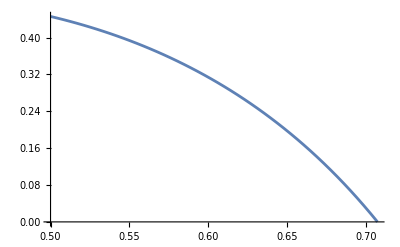
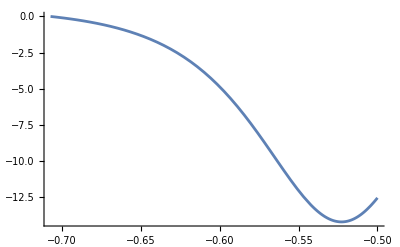

```mathematica
{Plot[(2 (47+476 ss+1764 ss^2+2375 ss^3-1528 ss^4-7442 ss^5-7296 ss^6-1576 ss^7+4208 ss^8+6064 ss^9+3264 ss^10+560 ss^11-160 ss^13))/((-1+ss)^2 (1+ss) (19+72 ss+84 ss^2+48 ss^3+44 ss^4)^2),{ss,1/2,1/√2}],Plot[(2 (47+476 ss+1764 ss^2+2375 ss^3-1528 ss^4-7442 ss^5-7296 ss^6-1576 ss^7+4208 ss^8+6064 ss^9+3264 ss^10+560 ss^11-160 ss^13))/((-1+ss)^2 (1+ss) (19+72 ss+84 ss^2+48 ss^3+44 ss^4)^2),{ss,-1/√2,-1/2}]}
```

Since in general it does not vanish, it does not have a single eigenvalue and a triple one.

Now, let us move to Class III.

```mathematica
UnsetCMetric[metric];
ClearxIdealCache["WeylConcomitants"]
```

```mathematica
linelement=(1-s)ω1^2+(1+s)ω2^2-2 ω3^2+dt^2;
linelement=Collect[linelement,{dt^2,dx^2,dy^2,dz^2,dx dz,dy dz},Simplify];
metricMatrix=
𝒶^2{
{Coefficient[linelement,dt^2],Coefficient[linelement,dt dx]/2,Coefficient[linelement,dt dy]/2,Coefficient[linelement,dt dz]/2},
{Coefficient[linelement,dx dt]/2,Coefficient[linelement,dx^2],Coefficient[linelement,dx dy]/2,Coefficient[linelement,dx dz]/2},
{Coefficient[linelement,dy dt]/2,Coefficient[linelement,dy dx]/2,Coefficient[linelement,dy^2],Coefficient[linelement,dy dz]/2},
{Coefficient[linelement,dz dt]/2,Coefficient[linelement,dz dx]/2,Coefficient[linelement,dz dy]/2,Coefficient[linelement,dz^2]}
};
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

We compute now the Ricci invariants q and Q and check the perfect fluid conditions

```mathematica
CD=CovDOfMetric[metric];
R=Ricci[CD];
r=R[a,-a]//Simplify;
S=R-1/4 r metric;
S2=HeadOfTensor[S[-a,i]S[-i,-b],{-a,-b}];
trS2=S2[a,-a];
S3=HeadOfTensor[S2[-a,i]S[-i,-b],{-a,-b}];
trS3=S3[a,-a];
q=-2 trS3/trS2//Simplify;
Q=S-1/4 q metric;
Q2=HeadOfTensor[Q[-a,i]Q[-i,-b],{-a,-b}];
```

```mathematica
Q2+q Q//Simplify
```

Zero

The first condition is fulfilled

```mathematica
v=CTensor[{Coefficient[ω3,dt],Coefficient[ω3,dx],Coefficient[ω3,dy],Coefficient[ω3,dz]},{-chart}];
 q Q[-i,-j]v[i]v[j]//FullSimplify
```

0

But the second one is not.

```mathematica
v1=CTensor[{Coefficient[ω1,dt],Coefficient[ω1,dx],Coefficient[ω1,dy],Coefficient[ω1,dz]},{-chart}];
```

Actually, we have that the eigenvector associated with the simple eigenvalue is ω1

```mathematica
v1=CTensor[{Coefficient[ω1,dt],Coefficient[ω1,dx],Coefficient[ω1,dy],Coefficient[ω1,dz]},{-chart}];
Q[-i,-j]-2v1[-i]v1[-j]
```

0

Which is space-like

```mathematica
v1[-i]v1[i]//Simplify
```

1/(a^2-s a^2)

#### Corrected metric

Now, we will check that the correct Osváth solutions indeed fulfill the perfect fluid condition (8).

Let us start with Class II.

First, we define the metric

```mathematica
UnsetCMetric[metric];
ClearxIdealCache["WeylConcomitants"]
```

```mathematica
linelement=(1-s)ω3^2+(1+s)ω2^2-2 ω1^2+(dt+√(1-2 s^2)ω1)^2;
linelement=Collect[linelement,{dt^2,dx^2,dy^2,dz^2,dx dz,dy dz},Simplify];
metricMatrix=
𝒶^2{
{Coefficient[linelement,dt^2],Coefficient[linelement,dt dx]/2,Coefficient[linelement,dt dy]/2,Coefficient[linelement,dt dz]/2},
{Coefficient[linelement,dx dt]/2,Coefficient[linelement,dx^2],Coefficient[linelement,dx dy]/2,Coefficient[linelement,dx dz]/2},
{Coefficient[linelement,dy dt]/2,Coefficient[linelement,dy dx]/2,Coefficient[linelement,dy^2],Coefficient[linelement,dy dz]/2},
{Coefficient[linelement,dz dt]/2,Coefficient[linelement,dz dx]/2,Coefficient[linelement,dz dy]/2,Coefficient[linelement,dz^2]}
};
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

We compute now the Ricci invariants q and Q and the 2-tensor defined by the first condition in (8)

```mathematica
CD=CovDOfMetric[metric];
R=Ricci[CD];
r=R[a,-a]//Simplify;
S=R-1/4 r metric;
S2=HeadOfTensor[S[-a,i]S[-i,-b],{-a,-b}]//Simplify;
trS2=S2[a,-a]//Simplify;
S3=HeadOfTensor[S2[-a,i]S[-i,-b],{-a,-b}];
trS3=S3[a,-a];
q=-2 trS3/trS2//Simplify;
Q=S-1/4 q metric;
Q2=HeadOfTensor[Q[-a,i]Q[-i,-b],{-a,-b}];
Q2+q Q//FullSimplify
```

Zero

The first condition is fulfilled. Let us check the second one. Now, ω1 is the time-like vector, so:

```mathematica
v=CTensor[{Coefficient[ω1,dt],Coefficient[ω1,dx],Coefficient[ω1,dy],Coefficient[ω1,dz]},{-chart}];
 q Q[-i,-j]v[i]v[j]//FullSimplify
```

(-1+4 s^2)/(8 (-1+s^2)^2 a^6)

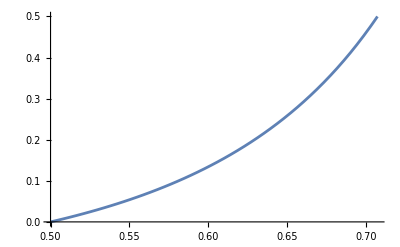
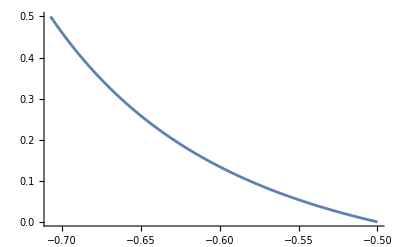

```mathematica
{Plot[(-1+4 ss^2)/(8 (-1+ss^2)^2),{ss,1/2,1/√2}],Plot[(-1+4 ss^2)/(8 (-1+ss^2)^2),{ss,-1/√2,-1/2}]}
```

The second condition is also fulfilled. Therefore, this is a perfect fluid solution.

Now that we have checked that our metric is a perfect fluid solution, let us determine its Petrov Type by using the xIdeal function that implements the algorithm in Fig. 1 (actually, we use the analog method with the Petrov Matrix since in this case it is faster, see https://arxiv.org/abs/2103.06158):

```mathematica
𝓋=√2 𝒶 v;
PetrovType[metric,Verbose->False,Method->"PetrovMatrix","Observer"->𝓋]
```

Type I

In this case, we will obtain the connection tensor H by obtaining the Weyl principal frame as indicated in Ferrando J J, Morales J A and S .13aez J A 2001 Class. Quantum Grav. 18 4939 and using Eq. (1). Let us do it step by step.

First, we get the necessary Weyl concomitants to write the characteristic equation

```mathematica
WeylCD=Weyl[CD]//FullSimplify;
epsilonmetric=epsilon[metric];
WeylDual=HeadOfTensor[1/2 epsilonmetric[-c,-d,-e,-f]WeylCD[e,f,-a,-b],{-c,-d,-a,-b}]//FullSimplify;
𝒲=1/2(WeylCD-I* WeylDual)//Simplify;
𝒬=HeadOfTensor[2𝓋[a]𝓋[c]𝒲[-a,-b,-c,-d],{-b,-d}]//Simplify;
𝒬2=HeadOfTensor[𝒬[-a,-b]𝒬[b,-c],{-a,-c}]//Simplify;
𝒬3=HeadOfTensor[𝒬2[-a,-c]𝒬[c,-d],{-a,-d}]//Simplify;
aa=𝒬2[-a,a]//Simplify;
bb=-𝒬3[-a,a]//FullSimplify;
```

Next, we solve the characteristic equation to get the self-dual Weyl eigenvalues

```mathematica
Solve[xx^3-1/2 aa xx-1/3 bb==0,xx]//FullSimplify
```

{{xx→-s^2/(3 (-1+s^2) a^2)},{xx→(-2 s^2+2 s^4-3 √2 √(s^2 (-1+s^2)^2 (-1+2 s^2)))/(12 (-1+s^2)^2 a^2)},{xx→(-2 s^2+2 s^4+3 √2 √(s^2 (-1+s^2)^2 (-1+2 s^2)))/(12 (-1+s^2)^2 a^2)}}

```mathematica
α1=-s^2/(3 (-1+s^2) 𝒶^2);
α2=(-2 s^2+2 s^4-3 I s(1- s^2) √2 √(1-2 s^2))/(12 (-1+s^2)^2 𝒶^2)//FullSimplify;
α3=(-2 s^2+2 s^4+3 I s(1-s^2) √2 √(1-2 s^2))/(12 (-1+s^2)^2 𝒶^2)//FullSimplify;
```

Now, for Petrov Type I metrics, we need to build the following projectors

```mathematica
$Assumptions=𝒶∈Reals&&y[]∈Reals&&s∈Reals;
```

```mathematica
𝒲2=HeadOfTensor[1/2 𝒲[-a,-b,-i,-j]𝒲[i,j,-c,-d],{-a,-b,-c,-d}]//FullSimplify;
𝒫11=𝒲2+α1 𝒲+(α1^2-1/2 aa)𝒢//FullSimplify;
𝒫22=𝒲2+α2 𝒲+(α2^2-1/2 aa)𝒢//FullSimplify;
𝒫22unitari=-𝒫22/(3 α2^2-aa/2)//FullSimplify;
𝒫33=𝒲2+α3 𝒲+(α3^2-1/2 aa)𝒢//FullSimplify;
𝒫33unitari=-𝒫33/(3 α3^2-aa/2)//FullSimplify;
```

Next, we need arbitrary bivectors to project them and get the canonical bivectors. We will build them out of the ω^i basis

```mathematica
$Assumptions=𝒶∈Reals&&y[]∈Reals&&s∈Reals&&s!=0&&s^2<1/4;
```

```mathematica
w1=CTensor[{Coefficient[ω1,dt],Coefficient[ω1,dx],Coefficient[ω1,dy],Coefficient[ω1,dz]},{-chart}];
w2=CTensor[{Coefficient[ω2,dt],Coefficient[ω2,dx],Coefficient[ω2,dy],Coefficient[ω2,dz]},{-chart}];
w3=CTensor[{Coefficient[ω3,dt],Coefficient[ω3,dx],Coefficient[ω3,dy],Coefficient[ω3,dz]},{-chart}];
w4=CTensor[{1,0,0,0},{-chart}];
X1=HeadOfTensor[w4[-a]w1[-b]-w4[-b]w1[-a],{-a,-b}]//FullSimplify;
X2=HeadOfTensor[w2[-a]w1[-b]-w2[-b]w1[-a],{-a,-b}]//FullSimplify;
Biv1=HeadOfTensor[𝒫11[-a,-b,-c,-d]X1[c,d],{-a,-b}]//FullSimplify;
Biv1=HeadOfTensor[(√2 Biv1[-a,-b])/(√(-Biv1[-i,-j]Biv1[i,j])),{-a,-b}]//FullSimplify;
Biv2=HeadOfTensor[𝒫22unitari[-a,-b,-c,-d]X2[c,d],{-a,-b}]//FullSimplify;
Biv2=HeadOfTensor[(-√2 Biv2[-a,-b])/(√(-Biv2[-i,-j]Biv2[i,j])),{-a,-b}]//FullSimplify;
Biv3=HeadOfTensor[𝒫33unitari[-a,-b,-c,-d]X2[c,d],{-a,-b}]//FullSimplify;
Biv3=HeadOfTensor[(-√2 Biv3[-a,-b])/(√(-Biv3[-i,-j]Biv3[i,j])),{-a,-b}]//FullSimplify;
```

Finally, we get the real two-forms associated with the canonical bivectors

```mathematica
U11=(√2)/2(Biv1+Dagger[Biv1])//FullSimplify;
U22=(√2)/2(Biv2+Dagger[Biv2])//FullSimplify;
U33=(√2)/2(Biv3+Dagger[Biv3])//FullSimplify;
```

and the Weyl principal frame as

```mathematica
P0=HeadOfTensor[1/2(metric[-a,-b]-U11[-a,-i]U11[i,-b]-U22[-a,-i]U22[i,-b]-U33[-a,-i]U33[i,-b]),{-a,-b}]//FullSimplify;
vv=(w1+w4+w2)/((-1+√(1-2 kk^2))/(√2 𝒶))//FullSimplify;
e00=HeadOfTensor[P0[-a,-i]vv[i],{-a}]//FullSimplify;
e00=HeadOfTensor[(-e00[-a])/(√(-e00[-i]e00[i])),{-a}]//FullSimplify;
e11=HeadOfTensor[U11[-a,-i]e00[i],{-a}]//FullSimplify;
e22=HeadOfTensor[U22[-a,-i]e00[i],{-a}]//FullSimplify;
e33=HeadOfTensor[U33[-a,-i]e00[i],{-a}]//FullSimplify;
```

This computation can actually be performed faster by hand using the non-coordinate frame of the ω^i and one gets the same result

```mathematica
e0=𝒶 √2 w1;
e1=𝒶 w4+𝒶 √(1-2 s^2)w1;
e2=𝒶(√(1+s)w2+√(1-s)w3)/√2;
e3=𝒶(√(1+s)w2-√(1-s)w3)/√2;
```

Any way, with this, the connection tensor H can be obtained as (1):

```mathematica
H=HeadOfTensor[-(1/2) (-(CD[a][e0[b]] e0[c]-CD[a][e0[c]] e0[b])+(CD[a][e1[b]] e1[c]-CD[a][e1[c]] e1[b])+(CD[a][e2[b]] e2[c]-CD[a][e2[c]] e2[b])+(CD[a][e3[b]] e3[c]-CD[a][e3[c]] e3[b])),{a,b,c}]//FullSimplify;
```

Now that we have the connection tensor H, we can apply the algorithm in Fig. 4. We start by using the xIdeal function that computes C^[1]:

```mathematica
C1=Simplify[HeadOfTensor[CD[-a][H[-b,-c,-d]]+H[-a,-b,i]H[-i,-c,-d]+H[-a,-c,j]H[-b,-j,-d]+H[-a,-d,k]H[-b,-c,-k],{-a,-b,-c,-d}]]
```

Zero

It vanishes, so we have a G_4/O_4. We could have also obtained this result by using the xIdeal function that gives the dimension of the isometry group of a metric if its associated connection tensor is known

```mathematica
IsometryGroupDimension[metric,H,Verbose->False]
```

G_4

Now we need to check the trace of H

```mathematica
trH=H[a,-a,-b]//Simplify
```

0

It vanishes, so the group is unimodular. However, q is positive but r is not

```mathematica
r
```

(3-4 s^2)/(2 (-1+s^2) a^2)

```mathematica
q
```

(1-4 s^2)/(2 (-1+s^2) a^2)

So this is not a spatially-homogeneous solution.

Now, let us move to Class III.

```mathematica
UnsetCMetric[metric];
ClearxIdealCache["WeylConcomitants"]
```

```mathematica
linelement=(1-s)ω3^2+(1+s)ω2^2-2 ω1^2+dt^2;
linelement=Collect[linelement,{dt^2,dx^2,dy^2,dz^2,dx dz,dy dz},Simplify];
metricMatrix=
𝒶^2{
{Coefficient[linelement,dt^2],Coefficient[linelement,dt dx]/2,Coefficient[linelement,dt dy]/2,Coefficient[linelement,dt dz]/2},
{Coefficient[linelement,dx dt]/2,Coefficient[linelement,dx^2],Coefficient[linelement,dx dy]/2,Coefficient[linelement,dx dz]/2},
{Coefficient[linelement,dy dt]/2,Coefficient[linelement,dy dx]/2,Coefficient[linelement,dy^2],Coefficient[linelement,dy dz]/2},
{Coefficient[linelement,dz dt]/2,Coefficient[linelement,dz dx]/2,Coefficient[linelement,dz dy]/2,Coefficient[linelement,dz^2]}
};
metric=CTensor[metricMatrix,{-chart,-chart}];
SetCMetric[metric,chart,SignatureOfMetric->{3,1,0}];
```

We compute now the Ricci invariants q and Q and check the perfect fluid conditions

```mathematica
CD=CovDOfMetric[metric];
R=Ricci[CD];
r=R[a,-a]//Simplify;
S=R-1/4 r metric;
S2=HeadOfTensor[S[-a,i]S[-i,-b],{-a,-b}];
trS2=S2[a,-a];
S3=HeadOfTensor[S2[-a,i]S[-i,-b],{-a,-b}];
trS3=S3[a,-a];
q=-2 trS3/trS2//Simplify;
Q=S-1/4 q metric;
Q2=HeadOfTensor[Q[-a,i]Q[-i,-b],{-a,-b}];
```

```mathematica
Q2+q Q//Simplify
```

Zero

```mathematica
v=CTensor[{Coefficient[ω1,dt],Coefficient[ω1,dx],Coefficient[ω1,dy],Coefficient[ω1,dz]},{-chart}];
 q Q[-i,-j]v[i]v[j]//FullSimplify
```

1/(2 a^6)

Both conditions are fulfilled.

Now that we have checked that our metric is a perfect fluid solution, let us determine its Petrov Type by using the xIdeal function that implements the algorithm in Fig. 1:

```mathematica
PetrovType[metric,Verbose->False]
```

Type D

Since this metric is of Petrov Type D, in order to obtain its connection tensor H we need to follow the algorithm in Fig. 3. Let us do it, step by step, explicitly. We start by obtaining δ_1:

```mathematica
W=Weyl[CD];
P=Q/q;
E1=HeadOfTensor[W[-a,-i,-b,-j]P[i,j],{-a,-b}]//Simplify;
E12=HeadOfTensor[E1[-a,i]E1[-i,-b],{-a,-b}]//Simplify;
trE12=E12[a,-a]//Simplify;
E13=HeadOfTensor[E12[-a,i]E1[-i,-b],{-a,-b}]//Simplify;
trE13=E13[a,-a]//Simplify;
δ1=trE12^3-6 trE13^2//Simplify
```

0

Since it vanishes, now we need to check wether r, q and ψ are constants or not:

```mathematica
r
```

-1/a^2

```mathematica
q
```

1/a^2

```mathematica
aa=xAct`xIdeal`Private`weylConcomitant["TraceWeylSelfDual2"][metric,Verbose->False];
bb=xAct`xIdeal`Private`weylConcomitant["TraceWeylSelfDual3"][metric,Verbose->False];
ψ=-bb/aa//Simplify
```

-1/(6 a^2)

The three of them are constant, so now we need to obtain E_2:

```mathematica
𝒢=xAct`xIdeal`Private`metricConcomitant["G2Form"][metric,Verbose->False];
𝒲=xAct`xIdeal`Private`weylConcomitant["WeylSelfDual"][metric,Verbose->False];
P1=HeadOfTensor[(2/3(1/ψ 𝒲-𝒢))[-a,-i,-b,-j]P[i,j],{-a,-b}]//Simplify;
v1=CTensor[{1,0,0,0},{-chart}];
e1=HeadOfTensor[P1[-a,i]v1[-i],{-a}]//Simplify;
ω=HeadOfTensor[-1/6 epsilon[metric][-a,-b,-c,-d](CD[b][P[c,-i]]P[i,d]),{-a}]//Simplify;
E2=HeadOfTensor[ω[i]ω[-i]P1[-a,-b]-ω[-a]ω[-b],{-a,-b}]//Simplify
```

Zero

It vanishes, so we need to compute δ_σ:

```mathematica
Σ=HeadOfTensor[-1/2(CD[-a][P[-b,-m]]+CD[-b][P[-a,-m]])P[m,-l],{-a,-b,-l}]//Simplify;
𝓍=HeadOfTensor[-Σ[-b,-l,-m]Σ[-c,l,m]Σ[b,c,a],{a}]//Simplify;
σ2=HeadOfTensor[-Σ[-a,-l,-m]Σ[-b,l,m],{-a,-b}]//Simplify;
ασ=σ2[a,-a]//Simplify;
δσ=ασ^3-6𝓍[a]𝓍[-a]//Simplify
```

-s^6/((-1+s^2)^3 a^6)

It does not vanish, so H=H_σ:

```mathematica
KK=1/δσ(3ασ  σ2+6Σ[-a,-b,-c]𝓍[c]+1/2 ασ^2(metric+P))//Simplify;
J=HeadOfTensor[CD[-a][Σ[b,-c,-d]]Σ[c,e,-f]P[d,f]epsilon[metric][-b,-e,-g,-h]KK[g,i]epsilon[metric][-i,-j,-k,-l]P[h,l],{-a,-j,-k}]//Simplify;
ℐ=HeadOfTensor[-CD[-a][P[i,-b]]P[-c,-i]+CD[-a][P[i,-c]]P[-b,-i],{-a,-b,-c}]//Simplify;
H=ℐ-J//Simplify;
```

Now that we have the connection tensor H, we can apply the algorithm in Fig. 4. We start by using the xIdeal function that computes C^[1]:

```mathematica
C1=Simplify[HeadOfTensor[CD[-a][H[-b,-c,-d]]+H[-a,-b,i]H[-i,-c,-d]+H[-a,-c,j]H[-b,-j,-d]+H[-a,-d,k]H[-b,-c,-k],{-a,-b,-c,-d}]]
```

Zero

It vanishes, so we have a G_4/O_4. We could have also obtained this result by using the xIdeal function that gives the dimension of the isometry group of a metric if its associated connection tensor is known

```mathematica
IsometryGroupDimension[metric,H,Verbose->False]
```

G_4

Now we need to check the trace of H

```mathematica
trH=H[a,-a,-b]//Simplify
```

0

It vanishes, so the group is unimodular. However, q is positive but r is not

```mathematica
r
```

-1/a^2

```mathematica
q
```

1/a^2

So this is not a spatially-homogeneous solution.